# Base method

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-4,30-4}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,3];
pyrf2=pyrFuncGen[line2,3];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}];
```

## Pyramidal Flow 1D

### See Plot

```mathematica
(* Function to plot flow solution *)
(* Input-> {pixel of interest, range of plot from p, {initial value for v1, initial value for v2}, {functions a, da, b, db}}*)
(* Output-> Plot with graphics solutions *)
seePlot[p_,q_,{v1_,v2_},{{a_,da_},{b_,db_}}]:=Block[{c},(
c=(a[p]+b[p])/2;
Show[
Plot[{a[x],b[x]},{x,p-q,p+q}],
Graphics[{
Point[{{p,c},{p,a[p]},{p,b[p]}}],
Point[{{p-v1,c},{p+v2,c}}],
Line[{{p,a[p]},{p,b[p]}}],
Line[{{p-v1,c},{p+v2,c}}]
}]
]
)];

seePlot::usage="
Function to plot flow solution
Input→ {p, q, {v1, v2}, {{a,da},{b,db}}}
Output-> a and b plot with v1 and v2 solutions
p= Pixel of interest
q= Range to plot from pixel of interest
v1= Solution for a
v2= Solution for b
{a, da}= {function of a, derivative of function of a}
{b, db}= {function of b, derivative of function of b}
";
```

### PyrUpgrade1D

```mathematica
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)

PyrUpgrade1D::usage="
Function to update values of v1 and v2.
Input→ [{v1,v2,status,___},p0,{{f1,df1},{f2,df2},threshold,mode}
Output-> {v1,v2,status,___}
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
e= counts the amount of constraints not met
p0= point of interest
{f1,df1}={function 1, derivative of function 1}
{f2,df2}={function 2, derivative of function 2}
threshold= threshold to respect magnitude constraint
";
```

### PyrFlow1D

```mathematica
PyrFlow1D::usage="
Function to update values of v1 and v2 over all levels of a function's pyramidal representation.
Input→ [i, p0, pyrfunctions, threshold]
Output-> {v1, v2, status, ___}
i= number of iterations
p0= point of interest
pyrfunctions= list with the dimensions of {pyrlvl, number of image(1 or 2), kind of function(f or df)}
where pyrlvl is the pyramidal level
threshold= threshold to respect magnitude constraint
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
e= Counts the amount of times the constraints were not met
";
```

## Graphics for All pixels

### All Pixel Values

```mathematica
lineTest[v0_,rangex_,pyrab_,threshold_,mode_]:=Block[{v1,v2,status},(
Table[
{v1,v2,status}=PyrFlow1D[10,x,pyrab,threshold,mode]
,{x,rangex}]
)]


lineTest[rangev0_,rangex_,pyrab_,threshold_,"ConstrainedNewMethod"]:=Block[{v1,v2,status},(
Table[
{v1,v2,status}=PyrFlow1D[10,x,rangev0,pyrab,threshold,"ConstrainedNewMethod"];
{v1,v2,status,x}
,{x,rangex}]
)]
```

#### Test

```mathematica
tes1=lineTest[Range[1,Length[line1]],pyrf12[[3;;3]],0.001,"OverConstrained"];
```

### See All pixels in line

```mathematica
seeAllLine[rangev0_,rangex_,pyrab_,threshold_,mode_]:=Block[{tRun,lineia,dlineia,lineib,dlineib,cTable,c,g0,i},(

tRun=lineTest[rangev0,rangex,pyrab,threshold,mode];

{lineia,dlineia}=pyrab[[1,1]];
{lineib,dlineib}=pyrab[[1,2]];

i=1;
cTable=Table[
c=(lineia[p]+lineib[p])/2;
g0=Graphics[{
PointSize[0.001],
Line[{{p,lineia[p]},{p,lineib[p]}}],
If[tRun[[i,3]]=="sign",Red,
If[tRun[[i,3]]=="mag",Purple,
If[tRun[[i,3]]=="flip",Orange,Black]]
],
Point[{p,c}],
{Arrowheads->Small,Arrow[{{p-tRun[[i,1]],c},{p+tRun[[i,2]],c}}]}
}];
i=i+1;
g0
,{p,rangex}];

Show[
Plot[{lineia[x],lineib[x]},{x,rangex[[1]],rangex[[-1]]},PlotLegends->{"ia","ib"},PlotLabel->mode],
cTable,
(*,
PlotLabel->info,*)
ImageSize->Scaled[0.5]
]
)]

seeAllLine[rangex_,pyrab_,threshold_,mode_]:=seeAllLine[{0.,0.},rangex,pyrab,threshold,mode]

seeAllLine::usage="
Input→ [rangex, {lvlmin,lvlmax}, pyrab, threshold]
Output-> Plot with solutions in rangex
";
```

#### Test

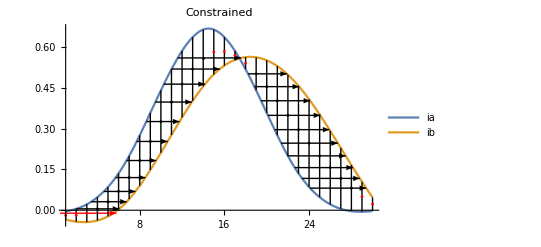

```mathematica
seeAllLine[Range[1,30],pyrf12[[4;;4]],0.001,"Constrained"]
```

## Graphics One pixel

### Pixel Iteration

```mathematica
(* Makes iterations by saving all the values *)

(* If you call without v0 (the initial motion), then it will be {0,0} *)
PyrFlow1DIter[i_, p0_, pyrfunctions_,threshold_,mode_]:=PyrFlow1DIter[i, p0,{0.,0.}, pyrfunctions,threshold,mode];

PyrFlow1DIter::usage="
Makes iterations with OverConstrained standards and saves all the values
Input→ [i, p0, pyrfunctions, threshold]
Output-> list with the dimensions of: {lvls, i, {v1, v2, status,e}}
i= number of iterations
p0= point of interest
pyrfunctions= list with the dimensions of {pyrlvl, number of image(1 or 2), kind of function(f or df)}
where pyrlvl is the pyramidal level
threshold= threshold to respect magnitude constraint
v1= Solution of f1
v2= Solution of f2
status= Status of the solution (ok, sign, mag, flip, converged)
e= Counts the amount of times constraints were not met
";
```

#### Test

```mathematica
iter=PyrFlow1DIter[10, 11,{0.,0.}, pyrf12[[1 ;;3]],0.001,"OverConstrained"];
```

### One level Pixel Iteration Graphics

```mathematica
(* Makes plots only for one level *)
(* input:{currentlvl, each iteration v, pixel of interest, pixel range for plots, functions of current lvl}*)
oneLevelPixelIterGraphics[lvl_,iter_, p0_,prange_, {{flineia_,dflineia_},{flineib_,dflineib_}},info_]:=Block[{c,iterTable},(

(* c values *)
c=(flineia[p0]+flineib[p0])/2;

iterTable=Table[
Labeled[
Show[
(* Plot Graphic *)
Plot[{flineia[x],flineib[x]},{x,p0-prange,p0+prange},PlotLegends->{"ia","ib"},PlotLabel->info],

Graphics[{
PointSize[0.01],
(* c line *)
Line[{{p0,flineia[p0]},{p0,flineib[p0]}}],
(*If[iter[[i,4]]==2,Blue,*)
If[iter[[i,3]]=="sign",Red,
If[iter[[i,3]]=="mag",Purple,
If[iter[[i,3]]=="flip",Orange,Black](*]*)
]],
(* c point *)
Point[{p0,c}],
{Arrowheads->Small,Arrow[{{p0-iter[[i,1]],c},{p0+iter[[i,2]],c}}]}
}],
ImageSize->Scaled[0.5]
],
(* Label *)
Style[Framed[GraphicsColumn[{
Row[{"Initial df= ", {NumberForm[dflineia[p0],3],NumberForm[dflineib[p0],3]}}],
Row[{"Current dv= ", {iter[[i,1]],iter[[i,2]]}}],
Row[{"Current iteration= ",i}],Row[{"Current level= ",lvl}]}]]]]
,{i,1,Length[iter]}]

)]

oneLevelPixelIterGraphics::usage="
Makes plots for the intermediate solutions of a pyramidal level
Input→ [lvl, iter, p0, prange, {{flineia, dflineia},{flineib, dflineib}}]
Output-> list with the dimensions of: {i, Plot of flineia and flineib with solution v1 and v2}
lvl= current pyramidal level
iter= solutions with the form {lvls, i, {v1, v2, status}
p0= pixel of interest
prange= range for plot from p0
{{flineia, dflineia},{flineib, dflineib}}= Current level functions 
";
```

#### Test

```mathematica
oneLevelPixelIterGraphics[3,iter[[1]], 11,5,pyrf12[[1]]];
```

### All levels pixel iteration Graphics

```mathematica
(* Makes graphics for all levels*)
(* iterations, pixel of interest, plot range from pixel, max lvl,lvl's functions, threshold}*)
pixelIterGraphics[i_, p0_,v0_,prange_, lvlmax_,pyrfunctions_,threshold_,mode_]:=Block[{iter},(
(* Makes iterations by saving all the values *)
iter=PyrFlow1DIter[i,p0,v0, pyrfunctions,threshold,mode];

Flatten[Table[
(* Makes plots only for one level *)
oneLevelPixelIterGraphics[lvlmax-j+1,iter[[j]], p0,prange,  pyrfunctions[[-j ;;-j]][[1]],mode]

,{j,1,Length[iter]}]]
)];

pixelIterGraphics[i_, p0_,prange_, lvlmax_,pyrfunctions_,threshold_,mode_]:=pixelIterGraphics[i, p0,{0.,0.},prange, lvlmax,pyrfunctions,threshold,mode];

pixelIterGraphics::usage="
Makes plots for the intermediate solutions of a pyramidal level
Input→ [i, p0, listv0, prange, maxlvl, pyrfunctions, threshold, mode]
Output-> list with the dimensions of: {lvls*i, Plot of flineia and flineib with solution v1 and v2}
";
```

#### Test

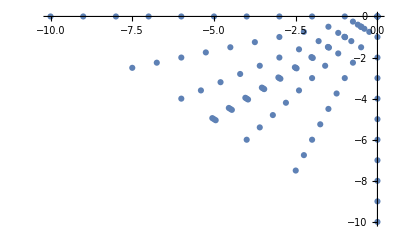

```mathematica
(* Creating list of values for v0 *)
rangev0=Range[-10,0];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
(* See list of values for v0 *)
ListPlot[listv0]
```

```mathematica
ListAnimate[pixelIterGraphics[10,11,listv0,3, 3,pyrf12[[1;;3]],0.01,"ConstrainedNewMethod"]]
```

$Aborted

## Graphics One pixel u1 and u2 convergence

### One Pixel u1 and u2 convergence

```mathematica
(* Makes graphics for all levels*)
(* iterations, pixel of interest, plot range from pixel, max lvl,lvl's functions, 
threshold}*)

pixelInitialValueGraphics[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,mode_]:=Block[{result,vx,vy},(

result=Table[(
Join[v,
PyrFlow1DIter[i,p0,v,pyrfunctions,threshold,mode][[-1,-1]]
]


),{v,listv0}];


Clear[dessin];
dessin[{u1_,u2_,v1_,v2_,"converged"}]:={Blue,Point[{u1,u2}],PointSize[0.05],Green,Point[{v1,v2}]};
dessin[{u1_,u2_,v1_,v2_,"mag"}]:={Purple,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,"sign"}]:={Red,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,"flip"}]:={Yellow,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,_}]:={Black,Point[{u1,u2}]};


Labeled[Graphics[{dessin/@result,{Thick,Black,Line[{{10,-10+sol},{-10,-(-10)+sol}}]}},PlotRange->{{-10,10},{-10,10}},Axes->True],mode]


)];

pixelInitialValueGraphics[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{result,vx,vy},(

result=Table[(
Join[v,
PyrFlow1DIter[i,p0,{v},pyrfunctions,threshold,"ConstrainedNewMethod"][[-1,-1]]
]


),{v,listv0}];


Clear[dessin];
dessin[{u1_,u2_,v1_,v2_,"converged"}]:={Blue,Point[{u1,u2}],PointSize[0.05],Green,Point[{v1,v2}]};
dessin[{u1_,u2_,v1_,v2_,"mag"}]:={Purple,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,"sign"}]:={Red,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,"flip"}]:={Yellow,Point[{u1,u2}]};
dessin[{u1_,u2_,v1_,v2_,_}]:={Black,Point[{u1,u2}]};


Labeled[Graphics[{dessin/@result,{Thick,Black,Line[{{10,-10+sol},{-10,-(-10)+sol}}]}},PlotRange->{{-10,10},{-10,10}},Axes->True],"ConstrainedNewMethod"]


)];

pixelInitialValueGraphics::usage="
Makes a plot to vizualise a map trying the initial values of {vx,vy}
and displays their status.
";
```

#### Test

```mathematica
lvlmin=1;
lvlmax=3;
e=0.001;
dis=4;
p=18;
```

```mathematica
rangev0=Range[-10,10];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
```

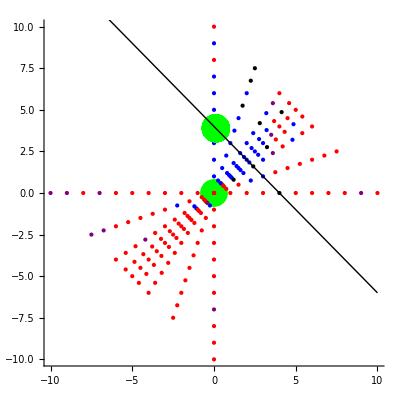
-Graphics-ConstrainedNewMethod

```mathematica
(*[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,"ConstrainedNewMethod"]*)

pixelInitialValueGraphics[10,p,listv0,dis,pyrf12[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

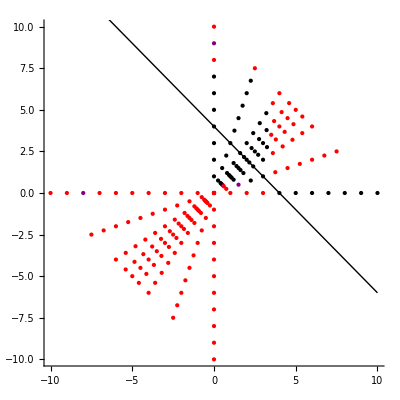
-Graphics-OverConstrained

```mathematica
(*[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,"ConstrainedNewMethod"]*)

pixelInitialValueGraphics[10,p,listv0,dis,pyrf12[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"OverConstrained"]
```

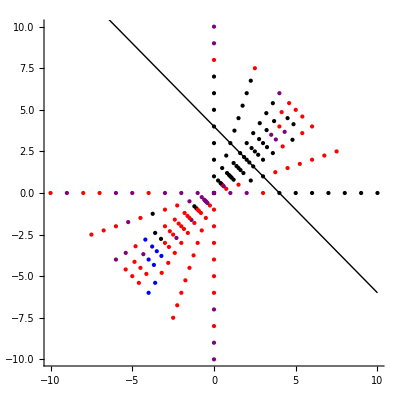
-Graphics-SemiConstrained

```mathematica
(*[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,"ConstrainedNewMethod"]*)

pixelInitialValueGraphics[10,p,listv0,dis,pyrf12[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"SemiConstrained"]
```

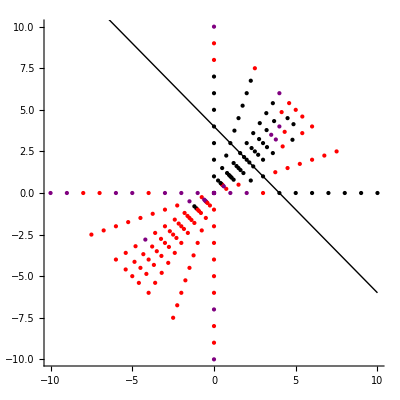
-Graphics-Constrained

```mathematica
(*[i_, p0_,listv0_,sol_,pyrfunctions_,threshold_,"ConstrainedNewMethod"]*)

pixelInitialValueGraphics[10,p,listv0,dis,pyrf12[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"Constrained"]
```